```mathematica
ClearAll["Global`*"]
Text["This section is to find the expressions of the constants. First we need to find the expression of Xt"]
h[s_]:= C1* Exp[k* s]+C2* Exp[-k* s]+ C3* Exp[-ρ* s];
e[s_]:= C1*k* Exp[k* s]-C2*k* Exp[-k* s]- C3*ρ* Exp[-ρ* s];
s1[v_]=V+RealAbs[v]
C3 =s1[v]/(4*β*ρ)+k^2/ρ^2;
k=√((γ*σ^2)/(2*β));
resAB = Solve[{h[0]==x0-v,h[T]==0 },{C1,C2}];
C1=resAB[[All,1,2]];
C2=resAB[[All,2,2]];
Text["Then we find the differentiable form"]
l[v_]=α*v^2 + α*s1[v]* Integrate[e[x]*Exp[-ρ* x], {x, 0, T}] + β*Integrate[e[x]^2, {x, 0, T}]- γ/2*σ^2*Integrate[h[x]^2, {x, 0, T}];
```

This section is to find the expressions of the constants. First we need to find the expression of Xt

V+RealAbs[v]

Then we find the differentiable form

```mathematica
V=5000;
x0=100000;
α=0.01;
β=0.1;
ρ=0.01;
σ=0.0000001;
γ=0.01;
T=1;
Text["Then we solve for v"]
resV = Solve[{D[l[v],v]==0},v];
v=resV[[All,1,2]];
v
```

Then we solve for v

{87304.4}

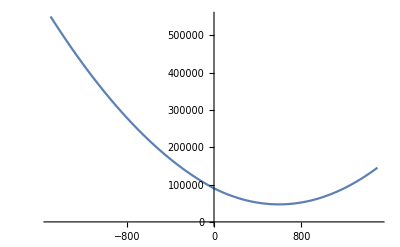

General::munfl: -0.818731 4.26292073327×10^-1229 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 4.05298×10^307 4.26292073327×10^-1229 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -0.818731 4.26292073327×10^-1229 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-

```mathematica
V=5000;
x0=1000;
α=0.01;
β=0.1;
ρ=0.1;
σ=0.75;
γ=0.01;
T=1;
Plot[l[v],{v,-1500,1500}]
```

```mathematica
q0=x0-v;
kQ =Sqrt[γ*σ^2/(2*α)];
qv[s_]=-q0*kQ*Cosh[kQ*(T-s)]/Sinh[kQ*T];
q[s_]=q0*Sinh[kQ*(T-s)]/Sinh[kQ*T];
l[v];
e[0];
p1=Plot[e[s],{s,0,1},PlotRange->Full,PlotStyle->Directive[Opacity[0.5],Green],PlotLegends->Placed[{"Optimal",None},{0.6,0.575}],AxesLabel->{"Time","Trading Rate"}];
p2=Plot[qv[s],{s,0,1},PlotRange->Full,PlotStyle->Directive[Opacity[0.5],Red],PlotLegends->Placed[{"TWAP",None},{0.6,0.5}],AxesLabel->{"Time","Trading Rate"}];
p3 =Plot[h[s],{s,0,1},PlotRange->Full,PlotStyle->Directive[Opacity[0.5],Green],PlotLegends->Placed[{"Optimal",None},{0.6,0.575}],AxesLabel->{"Time","Trading Curve"}];
p4=Plot[q[s],{s,0,1},PlotRange->Full,PlotStyle->Directive[Opacity[0.5],Red],PlotLegends->Placed[{"TWAP",None},{0.6,0.5}],AxesLabel->{"Time","Trading Curve"}];
Rasterize[Show[{p1,p2}]]
Rasterize[Show[{p3,p4}]]
Export["/home/hai.tran/Workspace/Latex/Auction_Note/images/ContinuousTradingRate.pdf",Rasterize[Show[{p1,p2}]]]
Export["/home/hai.tran/Workspace/Latex/Auction_Note/images/ContinuousTradingCurve.pdf",Rasterize[Show[{p3,p4}]]]
```

-Graphics-

-Graphics-

/home/hai.tran/Workspace/Latex/Auction_Note/images/ContinuousTradingRate.pdf

/home/hai.tran/Workspace/Latex/Auction_Note/images/ContinuousTradingCurve.pdf

```mathematica
n=100;
sampleData=List[];
For[i=0,i≤n,i++,σ=0.1+i*0.1;AppendTo[sampleData,{σ,v[[1]]/x0}]];
p5=ListLinePlot[sampleData,AxesLabel->{"σ","Auction Size"},PlotRange->All]
Export["/home/hai.tran/Workspace/Latex/Auction_Note/images/AuctionSizePct.pdf",Show[{p5}]]
```

```mathematica
v
```